{{0,1,0,1.5708,0,23.4612},{0.0020002,0.999986,-0.0138264,1.57078,-0.0196024,23.4612},{0.0040004,0.999945,-0.0276521,1.57072,-0.0392075,23.4612},10134,{1.9998,0.891939,-0.146082,-6.51509,5.26012,23.4612},{2,0.891909,-0.145447,-6.51403,5.26097,23.4612}}
 |  |  |  |

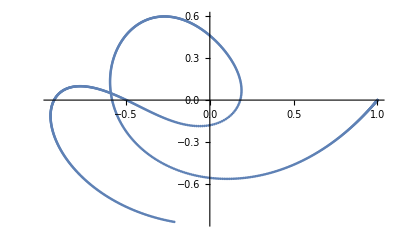

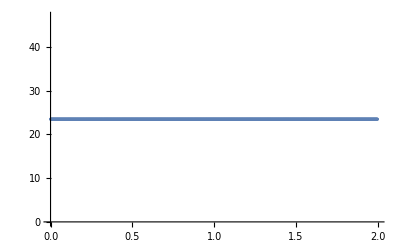

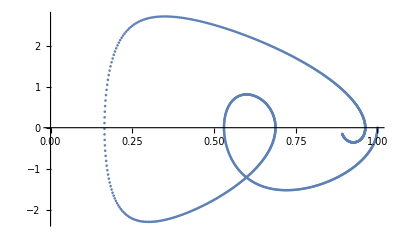

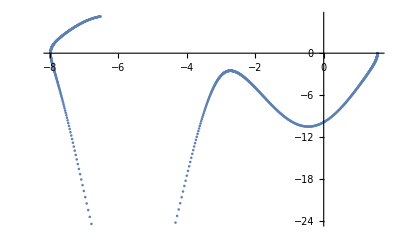

```mathematica
data=Import[NotebookDirectory[]<>"data","Data"]
xy=Table[{data[[i,2]]*Sin[data[[i,4]]],-data[[i,2]]*Cos[data[[i,4]]]},{i,1,1000}];
et=Table[{data[[i,1]],data[[i,6]]},{i,1,1000}];
vr=Table[{data[[i,2]],data[[i,3]]},{i,1,1000}];
vth=Table[{data[[i,4]],data[[i,5]]},{i,1,1000}];
ListPlot[xy]
ListPlot[et]
ListPlot[vr]
ListPlot[vth]
```